This compares MIDs simulated with OpenFLUX to our MID simulation, to ensure the models behave the same way

```mathematica
<<NilssonLab`MetabolicNetwork`
<<NilssonLab`ExtremePathways`
<<NilssonLab`AtomMap`
<<NilssonLab`EMUTracing`
<<NilssonLab`Visualization`
```

```mathematica
<<NilssonLab`OpenFLUX`
```

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]]
```

C:\code\liver-flux-models\Models\liverModel_2_openFluxExport

## Get model from DB

### Metabolic network

```mathematica
net=NetworkFromDB["liver-model-2"]
```

<MetabolicNetwork, 89 reactions>

### Atom map

```mathematica
atomMap=AtomMapsFromDB[net,{"C"}];
```

```mathematica
atomMap=RemoveUnreachable[net,atomMap];
Length[atomMap]
```

89

Consistency check. Missing data for cofactors is okay at this stage as long as they are removed below.

```mathematica
CheckAtomMap[atomMap]/.{{ri_Integer,s_List,p_List}:>{Reactions[net]⟦ri⟧,Union[Metabolite/@First/@s],Union[Metabolite/@First/@p]}}
```

{}

```mathematica
CheckAtomMap[atomMap]
```

{}

#### Boundary map

```mathematica
bmap=BoundaryAtomMaps[net,atomMap];
bmap//Length
```

35

### Symmetry

```mathematica
symmetry=GetSymmetryMap[atomMap]
```

{fum→{{1,2},{3,4}},succ→{{1,2},{3,4}}}

### Flux vector from OpenFLUX

```mathematica
fluxState=Block[{ofReactions,ofFluxes,reactionIds,bnet,nu,nr},
{ofReactions,ofFluxes}=Transpose[Import["FluxResults_liver-model-2_openflux.txt","TSV"]];
reactionIds= ReactionID/@Reactions[net];
bnet=BoundaryNetwork[net];
nu=Length[InputMetabolites[net]];
nr=Length[OutputMetabolites[net]];
FluxState@@Replace[
{reactionIds,
Table[StringJoin[r,"_R"],{r,reactionIds}],
Take[BoundaryFluxNames[bnet], nu],
Take[BoundaryFluxNames[bnet], -nr]} ,Append[Thread[Rule[ofReactions,ofFluxes]],_String->0],{2}]]
```

<FluxState, 89 reactions, 35 b. exch>

```mathematica
TableForm[Transpose[{ForwardFlux[fluxState],ReverseFlux[fluxState]}],
TableHeadings->{ ReactionID/@Reactions[net],{"fwd","rev"}}]
```

| fwd | rev
2AMACHYD | 10.1902 | 0
ACITL | 11.3402 | 0
ACOAHi | 0.230559 | 0
ACONTm | 4.97116 | 0.0271788
ACRNtm | 15.9198 | 0
ACS | 4.81016 | 0
ADK1 | 5.72059 | 0
AKGDm | 0.415655 | 0.0355542
AKGtm | 104.576 | 99.9897
ALATA_L | 0.078543 | 0
ARGN | 0.910429 | 0
ARGSL | 0.910429 | 0
ARGSS | 0.910429 | 0
ASPTA | 5.45646 | 0.449853
ASPTAm | 106.068 | 99.5328
ASPtm | 6.53504 | 0
ATPS4m | 39.8813 | 0
ATPtm | 114.702 | 79.88
CBPSam | 0.910429 | 0
CELLWORK | 0.26859 | 0
CITtm | 11.3402 | 0
CO2tm | 126.012 | 127.172
CRNtim | 15.9198 | 0
CSm | 16.2842 | 0
CSNATm | 15.9198 | 0
CSNATr | 15.9198 | 0
CYOOm | 8.86738 | 0
CYOR-u10m | 17.7348 | 0
ENO | 99.0383 | 101.512
FBA | 122.531 | 121.085
FBP | 0.242119 | 0
FUMm | 5.36598 | 0
FUMtm | 0.910429 | 0
G3PD1 | 103.118 | 98.8104
G6PPer | 4.39245 | 0
G6Pter | 4.39245 | 0
GAPD | 7.52703 | 0.328349
GHMT2r | 14.4981 | 14.4981
GLCter | 4.39245 | 0
GLNtm | 4.77967 | 0
GLUDxm | 98.4024 | 114.088
GLUNm | 7.10579 | 2.32612
GLUt2m | 92.1934 | 106.124
GLYCOGEN_BREAK | 2.14183 | 0
GLYK | 4.30762 | 0
GTHS | 6.80642 | 0
H2Oter | 4.39245 | 0
H2Otm | 79.5676 | 117.835
HCO3Em | 8.60412 | 0
HEX1 | 3.69615 | 0
Htm2 | 88.7696 | 103.102
ICDHxm | 93.5016 | 88.5576
LDH_L | 103.963 | 97.6388
MALtm | 13.835 | 0
MDH | 13.835 | 0
MDHm | 188.414 | 169.213
MMEm | 4.07545 | 0
MMMm | 4.07545 | 0
MMSAD1m | 4.07545 | 0
NADH2-u10m | 13.2792 | 0
NADH_REDOX | 1.01851 | 0
NDPK1 | 2.51181 | 0
NH4tm | 106.924 | 95.1076
O2tm | 8.86738 | 0
OCBTm | 0.910429 | 0
ORNt4m | 0.910429 | 0
PCm | 3.61824 | 0
PDHm | 0.364381 | 0
PEPCK | 2.51181 | 0
PFK | 1.68765 | 0
PGCD | 9.67191 | 0
PGI | 102.372 | 100.926
PGK | 100.941 | 93.7418
PGM | 99.0278 | 101.501
PGMT | 2.14183 | 0
PIt2m | 34.8224 | 0
PIter | 4.39245 | 0
PPA | 5.72059 | 0
PPCOACm | 4.07545 | 0
PROTDEG_ALA | 0.0260215 | 0
PROTDEG_ARG | 5.06407 | 0
PSERT | 9.67191 | 0
PSP_L | 9.67191 | 0
PYK | 0.0385764 | 0
PYRt2m | 99.9946 | 96.012
SERHL | 10.1902 | 0
SUCD1m | 4.45555 | 0
SUCOASm | 4.45555 | 0
TPI | 105.054 | 99.3009

```mathematica
TableForm[BoundaryFlux[fluxState],TableHeadings->{BoundaryFluxNames[BoundaryNetwork[net]],None}]
```

2mop_IN | 4.07545
ac_IN | 4.5796
ala-L_IN | 0.0525215
arg-L_IN | 7.82013
asp-L_IN | 11.3059
co2_IN | 10.8363
energy_IN | 9.79871
glc-D_IN | 12.5635
gln-L_IN | 4.77967
glucys_IN | 6.80642
gly_IN | 6.80642
glyc_IN | 4.30762
glycogen_IN | 2.14183
h2o_IN | 0.383233
h_IN | 2.41114
nh4_IN | 10.8866
o2_IN | 8.86738
pi_IN | 11.1466
prot_ala_IN | 0.0260215
prot_arg_IN | 5.06407
ser-L_IN | 1.41442
arg-L_OUT | 12.8842
asp-L_OUT | 11.9239
co2_OUT | 14.5079
energy_OUT | 10.0673
glc-D_OUT | 13.2598
glu-L_OUT | 9.34355
gthrd_OUT | 6.80642
h2o_OUT | 14.7412
h_OUT | 13.7056
lac-L_OUT | 6.3247
nh4_OUT | 9.26036
pi_OUT | 11.1466
ser-L_OUT | 0.896132
urea_OUT | 0.910429

```mathematica
TableForm[Chop[MassBalance[net,fluxState],10^-6],TableHeadings->{Metabolites[net],None}]
```

Metabolite[13dpg,Cytosol,Internal] | 0
Metabolite[2amac,Cytosol,Internal] | 0
Metabolite[2mop,Mitochondria,Uptake] | -4.07545
Metabolite[2pg,Cytosol,Internal] | 0
Metabolite[3pg,Cytosol,Internal] | 0
Metabolite[3php,Cytosol,Internal] | 0
Metabolite[ac,Cytosol,Uptake] | -4.5796
Metabolite[accoa,Cytosol,Internal] | 0
Metabolite[accoa,Mitochondria,Internal] | 0
Metabolite[acrn,Cytosol,Internal] | 0
Metabolite[acrn,Mitochondria,Internal] | 0
Metabolite[adp,Cytosol,Internal] | 0
Metabolite[adp,Mitochondria,Internal] | 0
Metabolite[akg,Cytosol,Internal] | 0
Metabolite[akg,Mitochondria,Internal] | 0
Metabolite[ala-L,Cytosol,Uptake] | -0.0525215
Metabolite[amp,Cytosol,Internal] | 0
Metabolite[arg-L,Cytosol,Free] | 5.06407
Metabolite[argsuc,Cytosol,Internal] | 0
Metabolite[asp-L,Cytosol,Free] | 0.618
Metabolite[asp-L,Mitochondria,Internal] | 0
Metabolite[atp,Cytosol,Internal] | 0
Metabolite[atp,Mitochondria,Internal] | 0
Metabolite[cbp,Mitochondria,Internal] | 0
Metabolite[cit,Cytosol,Internal] | 0
Metabolite[cit,Mitochondria,Internal] | 0
Metabolite[citr-L,Cytosol,Internal] | 0
Metabolite[citr-L,Mitochondria,Internal] | 0
Metabolite[co2,Cytosol,Free] | 3.6716
Metabolite[co2,Mitochondria,Internal] | 3.05553×10^-6
Metabolite[coa,Cytosol,Internal] | 0
Metabolite[coa,Mitochondria,Internal] | 0
Metabolite[crn,Cytosol,Internal] | 0
Metabolite[crn,Mitochondria,Internal] | 0
Metabolite[dhap,Cytosol,Internal] | 0
Metabolite[energy,Cytosol,Free] | 0.26859
Metabolite[f6p,Cytosol,Internal] | 0
Metabolite[fdp,Cytosol,Internal] | 0
Metabolite[ficytC,Mitochondria,Internal] | 0
Metabolite[focytC,Mitochondria,Internal] | 0
Metabolite[fum,Cytosol,Internal] | 0
Metabolite[fum,Mitochondria,Internal] | 0
Metabolite[g1p,Cytosol,Internal] | 0
Metabolite[g3p,Cytosol,Internal] | 0
Metabolite[g6p,Cytosol,Internal] | 0
Metabolite[g6p,EndoplasmicReticulum,Internal] | 0
Metabolite[gdp,Cytosol,Internal] | 0
Metabolite[glc-D,Cytosol,Free] | 0.6963
Metabolite[glc-D,EndoplasmicReticulum,Internal] | 0
Metabolite[gln-L,Cytosol,Uptake] | -4.77967
Metabolite[gln-L,Mitochondria,Internal] | 0
Metabolite[glucys,Cytosol,Uptake] | -6.80642
Metabolite[glu-L,Cytosol,Release] | 9.34355
Metabolite[glu-L,Mitochondria,Internal] | 0
Metabolite[gly,Cytosol,Uptake] | -6.80642
Metabolite[glyc3p,Cytosol,Internal] | 0
Metabolite[glyc,Cytosol,Uptake] | -4.30762
Metabolite[glycogen,Cytosol,Uptake] | -2.14183
Metabolite[gthrd,Cytosol,Release] | 6.80642
Metabolite[gtp,Cytosol,Internal] | 0
Metabolite[h2o,Cytosol,Free] | 14.358
Metabolite[h2o,Mitochondria,Internal] | -3.05553×10^-6
Metabolite[h2o,EndoplasmicReticulum,Internal] | 0
Metabolite[h,Cytosol,Free] | 11.2945
Metabolite[hco3,Mitochondria,Internal] | 0
Metabolite[h_ims,Mitochondria,Internal] | 0
Metabolite[h,Mitochondria,Internal] | 6.11107×10^-6
Metabolite[icit,Mitochondria,Internal] | 0
Metabolite[lac-L,Cytosol,Release] | 6.3247
Metabolite[mal-L,Cytosol,Internal] | 0
Metabolite[mal-L,Mitochondria,Internal] | 0
Metabolite[mlthf,Cytosol,Internal] | 0
Metabolite[mmcoa-R,Mitochondria,Internal] | 0
Metabolite[mmcoa-S,Mitochondria,Internal] | 0
Metabolite[nad,Cytosol,Internal] | 0
Metabolite[nadh,Cytosol,Internal] | 0
Metabolite[nadh,Mitochondria,Internal] | 6.11107×10^-6
Metabolite[nad,Mitochondria,Internal] | -6.11107×10^-6
Metabolite[nh4,Cytosol,Free] | -1.62624
Metabolite[nh4,Mitochondria,Internal] | 0
Metabolite[o2,Cytosol,Uptake] | -8.86738
Metabolite[o2,Mitochondria,Internal] | 0
Metabolite[oaa,Cytosol,Internal] | 0
Metabolite[oaa,Mitochondria,Internal] | 0
Metabolite[orn,Cytosol,Internal] | 0
Metabolite[orn,Mitochondria,Internal] | 0
Metabolite[pep,Cytosol,Internal] | 0
Metabolite[pi,Cytosol,Free] | 0
Metabolite[pi,Mitochondria,Internal] | 0
Metabolite[pi,EndoplasmicReticulum,Internal] | 0
Metabolite[ppcoa,Mitochondria,Internal] | 0
Metabolite[ppi,Cytosol,Internal] | 0
Metabolite[prot_ala,Cytosol,Uptake] | -0.0260215
Metabolite[prot_arg,Cytosol,Uptake] | -5.06407
Metabolite[pser-L,Cytosol,Internal] | 0
Metabolite[pyr,Cytosol,Internal] | 0
Metabolite[pyr,Mitochondria,Internal] | 0
Metabolite[q10h2,Mitochondria,Internal] | 0
Metabolite[q10,Mitochondria,Internal] | 0
Metabolite[ser-L,Cytosol,Free] | -0.518288
Metabolite[succ,Mitochondria,Internal] | 0
Metabolite[succoa,Mitochondria,Internal] | 0
Metabolite[thf,Cytosol,Internal] | 0
Metabolite[urea,Cytosol,Release] | 0.910429

Import as EMU flux vector

```mathematica
(*emuFluxVector=Block[{ofReactions,ofFluxes,emuFluxNames},
{ofReactions,ofFluxes}=Transpose[Import["FluxResults_liver-model-2_openflux_221005.txt","TSV"]];
emuFluxNames= EMUFluxMap[net,"reactions"];
Replace[
StringReplace[emuFluxNames,{"_f"->"","_r"->"_R"}],
Thread[Rule[ofReactions,ofFluxes]],{1}]]*)
```

### OpenFLUX Simulated MIDs and targets

TODO: this should be part of an openflux import function

<FluxState, 89 reactions, 35 b. exch>

We here assume the Openflux MIDs are for entire metabolites.

```mathematica
openFluxMIDs=Cases[
Import["MIDResults_liver-model-2_openflux.txt","TSV"],
{met_String,__}/;!StringMatchQ[met,"*_i"]];
openFluxMIDs=SplitBy[openFluxMIDs,First];
openFluxMIDs=Thread[Rule[
Replace[
StringReplace[openFluxMIDs⟦All,1,1⟧,{"ala_L"->"ala-L","arg_L"->"arg-L","asp_L"->"asp-L","citr_L"->"citr-L","glc_D"->"glc-D","gln_L"->"gln-L","glu_L"->"glu-L","mal_L"->"mal-L","mmcoa_S"->"mmcoa-S","ser_L"->"ser-L"}],
Table[Rule[MetaboliteShortName[Metabolite[e]],e],{e,MetaboliteEMUs[atomMap]}],
{1}],
openFluxMIDs⟦All,All,3⟧]];
```

```mathematica
targets=First/@openFluxMIDs
```

{<13dpg_c{(123)}>,<2pg_c{(123)}>,<3pg_c{(123)}>,<ac_c{(12)}>,<accoa_c{(1c)}>,<accoa_m{(1c)}>,<acrn_c{(17)}>,<acrn_m{(17)}>,<akg_c{(12345)}>,<akg_m{(12345)}>,<ala-L_c{(123)}>,<arg-L_c{(123456)}>,<asp-L_c{(1234)}>,<asp-L_m{(1234)}>,<citr-L_c{(123456)}>,<citr-L_m{(123456)}>,<co2_c{(1)}>,<co2_m{(1)}>,<dhap_c{(123)}>,<f6p_c{(123456)}>,<fdp_c{(123456)}>,<fum_m{(1234)}>,<g3p_c{(123)}>,<g6p_c{(123456)}>,<glc-D_c{(123456)}>,<glc-D_r{(123456)}>,<gln-L_c{(12345)}>,<gln-L_m{(12345)}>,<glu-L_c{(12345)}>,<glu-L_m{(12345)}>,<gly_c{(12)}>,<glyc3p_c{(123)}>,<mal-L_c{(1234)}>,<mal-L_m{(1234)}>,<mmcoa-S_m{(1cno)}>,<oaa_c{(1234)}>,<oaa_m{(1234)}>,<orn_c{(12345)}>,<orn_m{(12345)}>,<pep_c{(123)}>,<pyr_c{(123)}>,<ser-L_c{(123)}>,<succoa_m{(34fg)}>}

```mathematica
Cases[targets,Except[_EMU]]
```

{}

## EMU model

### EMU decomposition

Find EMU reactions (this takes some time)

```mathematica
emuReactions=EMUAlgorithm[net,atomMap,bmap,{"C"},targets,symmetry];
Length[emuReactions]
```

964

```mathematica
emuReactionNames=EMUFluxMap[net,"reactions"];
```

Reactions producing a given metabolite

```mathematica
Sort[Cases[emuReactions,
EMUReaction[ri_Integer,s_EMU,p:EMU[Metabolite["arg-L",__],_],c_]:>EMUReaction[emuReactionNames⟦ri⟧,s,p,c]]]//TableForm
```

EMUReaction[arg-L_IN,<arg-L_i{(12345)}>,<arg-L_c{(12345)}>,1]
EMUReaction[arg-L_IN,<arg-L_i{(123456)}>,<arg-L_c{(123456)}>,1]
EMUReaction[ARGSL_f,<argsuc_c{(12358)}>,<arg-L_c{(12345)}>,1]
EMUReaction[ARGSL_f,<argsuc_c{(12358a)}>,<arg-L_c{(123456)}>,1]
EMUReaction[PROTDEG_ARG_f,<prot_arg_c{(12345)}>,<arg-L_c{(12345)}>,1]
EMUReaction[PROTDEG_ARG_f,<prot_arg_c{(123456)}>,<arg-L_c{(123456)}>,1]

```mathematica
Position[emuReactionNames,"OCBTm_f"]
```

{{86}}

```mathematica
Cases[emuReactions,EMUReaction[80,__]]//TableForm
```

EMUReaction[80,<2mop_m{(4)}>,<co2_m{(1)}>,1]
EMUReaction[80,<2mop_m{(123)}>,<ppcoa_m{(14f)}>,1]
EMUReaction[80,<2mop_m{(2)}>,<ppcoa_m{(f)}>,1]
EMUReaction[80,<2mop_m{(13)}>,<ppcoa_m{(14)}>,1]
EMUReaction[80,<2mop_m{(1)}>,<ppcoa_m{(1)}>,1]
EMUReaction[80,<2mop_m{(3)}>,<ppcoa_m{(4)}>,1]
EMUReaction[80,<2mop_m{(12)}>,<ppcoa_m{(1f)}>,1]

Reactions with non-unity coefficients (due to equivalence classes)

```mathematica
Sort[Cases[emuReactions,
EMUReaction[ri_Integer,s_EMU,p_EMU,c:Except[1]]:>EMUReaction[emuReactionNames⟦ri⟧,s,p,c]]]//TableForm
```

EMUReaction[ARGSL_f,<argsuc_c{(4)}>,<fum_c{(1)|(2)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(6)}>,<fum_c{(1)|(2)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(7)}>,<fum_c{(3)|(4)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(9)}>,<fum_c{(3)|(4)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(47)}>,<fum_c{(13)|(24)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(69)}>,<fum_c{(13)|(24)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(467)}>,<fum_c{(123)|(124)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(469)}>,<fum_c{(123)|(124)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(3)}>,<succ_m{(1)|(2)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(4)}>,<succ_m{(1)|(2)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(f)}>,<succ_m{(3)|(4)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(g)}>,<succ_m{(3)|(4)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(3f)}>,<succ_m{(13)|(24)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(4g)}>,<succ_m{(13)|(24)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(34f)}>,<succ_m{(123)|(124)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(34g)}>,<succ_m{(123)|(124)}>,1/2]

```mathematica
Union[Dimensions/@emuReactions]
```

{{1},{2},{3},{4},{5},{6}}

```mathematica
RandomSample[emuReactions,10]
```

{EMUReaction[58,<g3p_c{(2)}>,<13dpg_c{(1)}>,1],EMUReaction[47,<accoa_c{(1c)}>,<acrn_c{(17)}>,1],EMUReaction[51,<fdp_c{(1)}>,<g3p_c{(2)}>,1],EMUReaction[42,<cit_m{(1)}>,<cit_c{(1)}>,1],EMUReaction[13,<glycogen_i{(456)}>,<glycogen_c{(456)}>,1],EMUReaction[29,<akg_m{(1)}>,<succoa_m{(4)}>,1],EMUReaction[5,<asp-L_i{(124)}>,<asp-L_c{(124)}>,1],EMUReaction[13,<glycogen_i{(123)}>,<glycogen_c{(123)}>,1],EMUReaction[71,<glc-D_c{(45)}>,<g6p_c{(45)}>,1],EMUReaction[65,<glycogen_c{(2)}>,<g1p_c{(5)}>,1]}

Number of EMUs

```mathematica
emus=Union[Cases[emuReactions,EMUReaction[_,_,e_EMU,_]->e]];
emus//Length
```

497

Size of EMU equivalence classes

```mathematica
Tally[Length/@AtomNumbers/@emus]
```

{{1,485},{2,12}}

```mathematica
Complement[targets,emus]
```

{}

Total number of variables (MI fractions)

```mathematica
Total[Map[(Times@@#&),(Dimensions/@emus)+1]]
```

1497

### Generate equation systems

```mathematica
emuEq=EMUSystem[emuReactions,NumberOfFluxes[EMUFluxMap[net]]];
```

```mathematica
TableForm[emuEq,TableHeadings->Automatic]
```

1 | <EMUEquation (1), 217 internals, 42 substrates, 0 condensations >
2 | <EMUEquation (2), 150 internals, 27 substrates, 6 condensations >
3 | <EMUEquation (3), 78 internals, 13 substrates, 5 condensations >
4 | <EMUEquation (4), 24 internals, 2 substrates, 4 condensations >
5 | <EMUEquation (5), 15 internals, 3 substrates, 2 condensations >
6 | <EMUEquation (6), 13 internals, 4 substrates, 2 condensations >

### Specify input isotopomers (tracers)

```mathematica
<<NilssonLab`IsotopeDistributions`
```

List the input metabolites that have atom information; for these the isotope distributions must be specified.

```mathematica
substrateDist=ImportMixtureID["substrate-distributions.txt"]
```

{2mop_i→NaturalIsotopomerDistribution[{4},{0.98}],ac_i→NaturalIsotopomerDistribution[{2},{0.0107}],ala-L_i→NaturalIsotopomerDistribution[{3},{0.98}],arg-L_i→NaturalIsotopomerDistribution[{6},{0.98}],asp-L_i→NaturalIsotopomerDistribution[{4},{0.98}],co2_i→NaturalIsotopomerDistribution[{1},{0.0107}],glc-D_i→NaturalIsotopomerDistribution[{6},{0.98}],gln-L_i→NaturalIsotopomerDistribution[{5},{0.98}],glucys_i→NaturalIsotopomerDistribution[{8},{0.0107}],gly_i→NaturalIsotopomerDistribution[{2},{0.98}],glyc_i→NaturalIsotopomerDistribution[{3},{0.0107}],glycogen_i→NaturalIsotopomerDistribution[{6},{0.0107}],prot_ala_i→NaturalIsotopomerDistribution[{3},{0.0107}],prot_arg_i→NaturalIsotopomerDistribution[{6},{0.0107}],ser-L_i→NaturalIsotopomerDistribution[{3},{0.98}]}

Calculate MIDs for network substrate EMUs

```mathematica
irList=Table[
Rule[e,Total[Table[
PDF[MarginalizeToMID[
FragmentIsotopomerDistribution[
MetaboliteShortName[Metabolite[e]]/.substrateDist,a]],
x],
{a,AtomNumbers[e]},{x,Tuples[Map[Range[0,Length[#]]&,a]]}]]],
{e,Flatten[SubstrateEMUs/@emuEq]}];
```

## Simulate steady-state mass isotopomer data

```mathematica
emuSol=EMUSimulate[emuEq,irList,EMUFluxMap[net][fluxState]]
```

<EMUSolution, 6 subsystems>

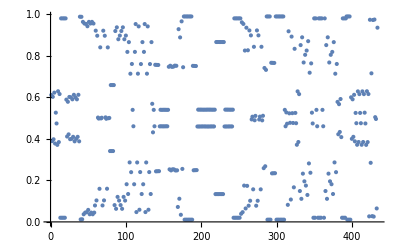
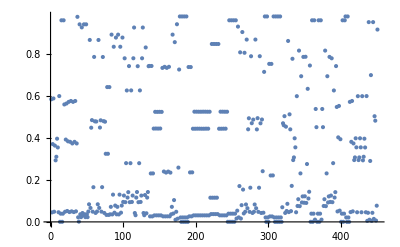
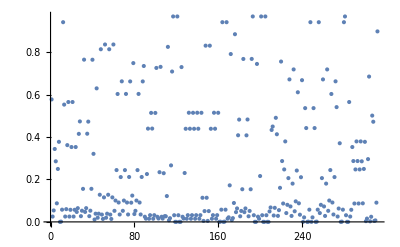
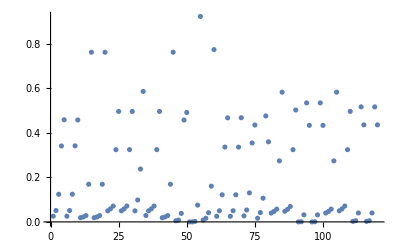
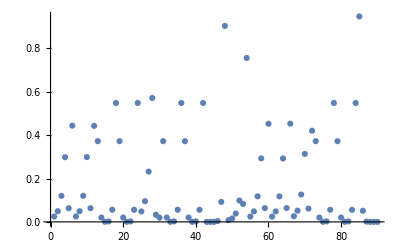
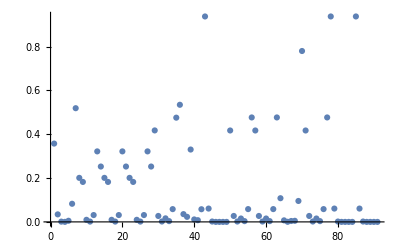

```mathematica
Table[
ListPlot[Flatten[InternalMIDs[emuSol,k]]],
{k,Length[emuEq]}]
```

```mathematica
TableForm[emuSol[targets],TableHeadings->{targets,None}]
```

```mathematica
With[{e=SubstrateEMUs[emuEq⟦6⟧]},
TableForm[emuSol[e],TableHeadings->{e,None}]]
```

<arg-L_i{(123456)}> | 6.4×10^-11 | 1.8816×10^-8 | 2.30496×10^-6 | 0.000150591 | 0.00553421 | 0.10847 | 0.885842
<glc-D_i{(123456)}> | 6.4×10^-11 | 1.8816×10^-8 | 2.30496×10^-6 | 0.000150591 | 0.00553421 | 0.10847 | 0.885842
<glycogen_i{(123456)}> | 0.937493 | 0.060838 | 0.00164502 | 0.0000237228 | 1.92434×10^-7 | 8.32527×10^-10 | 1.50073×10^-12
<prot_arg_i{(123456)}> | 0.937493 | 0.060838 | 0.00164502 | 0.0000237228 | 1.92434×10^-7 | 8.32527×10^-10 | 1.50073×10^-12

```mathematica
With[{e=InternalEMUs[emuEq⟦6⟧]},
TableForm[emuSol[e],TableHeadings->{e,None}]]
```

<arg-L_c{(123456)}> | 0.35742 | 0.0343711 | 0.00123456 | 0.000190268 | 0.00520037 | 0.0827282 | 0.518856
<argsuc_c{(12358a)}> | 0.200945 | 0.182385 | 0.00953587 | 0.00145745 | 0.0312578 | 0.321773 | 0.252646
<citr-L_c{(123456)}> | 0.200945 | 0.182385 | 0.00953587 | 0.00145745 | 0.0312578 | 0.321773 | 0.252646
<citr-L_m{(123456)}> | 0.200945 | 0.182385 | 0.00953587 | 0.00145745 | 0.0312578 | 0.321773 | 0.252646
<f6p_c{(123456)}> | 0.417425 | 0.0271257 | 0.00181276 | 0.0161971 | 0.00350073 | 0.0582789 | 0.47566
<fdp_c{(123456)}> | 0.534461 | 0.0354458 | 0.023062 | 0.330239 | 0.0112075 | 0.00779182 | 0.0577929
<g1p_c{(123456)}> | 0.937493 | 0.060838 | 0.00164502 | 0.0000237228 | 1.92434×10^-7 | 8.32527×10^-10 | 1.50073×10^-12
<g6p_c{(123456)}> | 0.417148 | 0.027106 | 0.0017625 | 0.0154544 | 0.00348251 | 0.0583983 | 0.476648
<g6p_r{(123456)}> | 0.417148 | 0.027106 | 0.0017625 | 0.0154544 | 0.00348251 | 0.0583983 | 0.476648
<glc-D_c{(123456)}> | 0.108062 | 0.00702185 | 0.000458285 | 0.00411505 | 0.00500271 | 0.0954993 | 0.77984
<glc-D_r{(123456)}> | 0.417148 | 0.027106 | 0.0017625 | 0.0154544 | 0.00348251 | 0.0583983 | 0.476648
<glycogen_c{(123456)}> | 0.937493 | 0.060838 | 0.00164502 | 0.0000237228 | 1.92434×10^-7 | 8.32527×10^-10 | 1.50073×10^-12
<prot_arg_c{(123456)}> | 0.937493 | 0.060838 | 0.00164502 | 0.0000237228 | 1.92434×10^-7 | 8.32527×10^-10 | 1.50073×10^-12

### Compare MIDs to Openflux

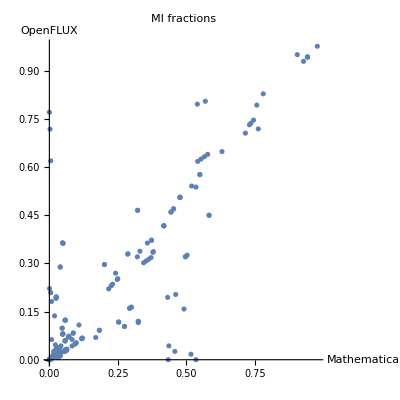

```mathematica
ListPlot[
Transpose[Flatten/@{emuSol[targets],targets/.openFluxMIDs}],
AxesLabel->{"Mathematica","OpenFLUX"},PlotLabel->"MI fractions",AspectRatio->1]
```

```mathematica
Position[emuSol[targets]-(targets/.openFluxMIDs),x_/;x<-0.5]
```

{{22,1},{35,1},{43,1}}

```mathematica
targets⟦22⟧
```

<fum_m{(1234)}>

```mathematica
{emuSol[targets],targets/.openFluxMIDs}⟦All,22⟧
```

{{0.00516802,0.00814995,0.0381759,0.457524,0.490982},{0.619903,0.181488,0.0146451,0.0259867,0.157977}}